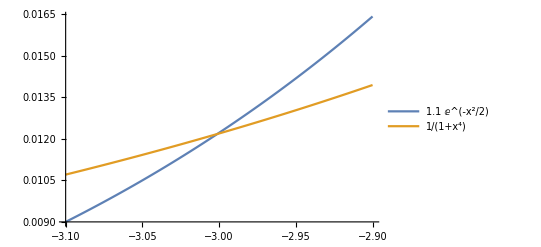

```mathematica
Plot[{1.1 ⅇ^(-x^2/2),1/(1+x^4)},{x,-3.1,-2.9},PlotLegends->"Expressions"]
```

```mathematica
Export["/Users/joey/Downloads/F&p.pdf",Plot[{1.1 ⅇ^(-x^2/2),1/(1+x^4)},{x,-4,4},PlotLegends->"Expressions"]]
```

/Users/joey/Downloads/F&p.pdf

```mathematica
N[1.1 ⅇ^(-x^2/2)-1/(1+x^4)/.x->3,5]
```

0.0000247742

```mathematica
N[Integrate[1/(1+x^4),{x,-3,3}],10]
```

2.196879736

```mathematica
Sum[0.01/(1+x^4),{x,-2.995,2.995,0.01}]
```

2.19688